## Chapter 9 3D Printing

### Section 9.3

```mathematica
ParametricPlot3D[{Cos[t],Sin[t],.1t},{t,0,6π},PlotStyle->Tube[.2],MaxRecursion->0,PlotRange->All]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[t],Sin[t],.1t},{t,0,6π},PlotStyle->Tube[.2],MaxRecursion->0,PlotRange->All,PlotPoints->13]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[t],Sin[t],.1t},{t,0,6π},PlotStyle->Tube[.2],MaxRecursion->0,PlotRange->All,PlotPoints->130]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[t],Sin[t],.1t},{t,0,6π},PlotStyle->Tube[.2,PlotPoints->4],MaxRecursion->0,PlotRange->All,PlotPoints->130]
```

-Graphics3D-

The PlotPoints setting in the Tube controls the shape of the cross-section (3 for triangle, 4 for square, etc.). The PlotPoints setting for ParametricPlot3D controls the number of segments into which the parameterized curve is partitioned.

```mathematica
ParametricPlot3D[{Cos[t],Sin[t],.1t},{t,0,6π},PlotStyle->Tube[.2,PlotPoints->24],MaxRecursion->0,PlotRange->All,PlotPoints->130]//DiscretizeGraphics
```

-Graphics3D-

Note the slight gap where the curve closes up. We address this in parts b and c.

```mathematica
ParametricPlot3D[{Cos[t],Sin[t],u},{t,0,2Pi},{u,0,1},PlotStyle->Thickness[.2],Mesh->All,MaxRecursion->0]
```

-Graphics3D-

We added (half of thickness)*√2 to the interval [0,2π] for t so things close up nicely.

```mathematica
ParametricPlot3D[{Cos[t],Sin[t],u},{t,0,2Pi+.141},{u,0,1},PlotStyle->Thickness[.2],Mesh->All,MaxRecursion->0,PlotPoints->5]
```

-Graphics3D-

We added .1 to the interval [0,2π] for t so things close up nicely.

```mathematica
ParametricPlot3D[{Cos[t],Sin[t],u},{t,0,2Pi+.1},{u,0,1},PlotStyle->Thickness[.2],Mesh->All,MaxRecursion->0,PlotPoints->{20,5}]
```

-Graphics3D-

### Section 9.5

Prior to version 12, the non-triangular faces are all removed from the mesh. Evidently, without a second argument to limit its scope, FindMeshDefects removes such faces before performing other diagnostics, such as face orientation. In version 12 and later, RepairMesh (appropriately) finds no defects with the mesh, and no changes are made.

```mathematica
v=PolyhedronData["Icosidodecahedron","VertexCoordinates"];
f=Select[PolyhedronData["Icosidodecahedron","FaceIndices"],ContainsNone[#,Flatten[Position[v,{_,_,_?Positive}],1]]&];
inner=MeshRegion[v,Polygon[f]];
outer=MeshRegion[1.2v,Polygon[f]];
union=RegionUnion[inner,outer];
bowlMesh=MeshRegion[MeshCoordinates[union],Join[MeshCells[union,2],Polygon/@{{1,21,30,10},{10,30,37,17},{17,37,38,18},{18,38,31,11},{11,31,22,2},{2,22,34,14},{14,34,36,16},{16,36,35,15},{15,35,33,13},{13,33,21,1}}]]
```

-Graphics3D-

```mathematica
RepairMesh[bowlMesh]
```

-Graphics3D-

```mathematica
Clear[v,f,inner,outer,union,bowlMesh]
```

Just extend the example with two cubes provided in this section.

```mathematica
vertices=N[Entity["Polyhedron","CubeFiveCompound"]["VertexCoordinates"]];
faces=Entity["Polyhedron","CubeFiveCompound"]["Faces"];
```

```mathematica
cube1=BoundaryMeshRegion[vertices,Polygon[faces⟦1;;6⟧]];
cube2=BoundaryMeshRegion[vertices,Polygon[faces⟦7;;12⟧]];
cube3=BoundaryMeshRegion[vertices,Polygon[faces⟦13;;18⟧]];
cube4=BoundaryMeshRegion[vertices,Polygon[faces⟦19;;24⟧]];
cube5=BoundaryMeshRegion[vertices,Polygon[faces⟦25;;30⟧]];
fiveCubes=RegionBoundary[RegionUnion[cube1,cube2,cube3,cube4,cube5]]
```

-Graphics3D-

Just replace RegionUnion above with RegionIntersection. The result is a rhombic triacontahedron.

```mathematica
vertices=N[Entity["Polyhedron","CubeFiveCompound"]["VertexCoordinates"]];
faces=Entity["Polyhedron","CubeFiveCompound"]["Faces"];
```

```mathematica
cube1=BoundaryMeshRegion[vertices,Polygon[faces⟦1;;6⟧]];
cube2=BoundaryMeshRegion[vertices,Polygon[faces⟦7;;12⟧]];
cube3=BoundaryMeshRegion[vertices,Polygon[faces⟦13;;18⟧]];
cube4=BoundaryMeshRegion[vertices,Polygon[faces⟦19;;24⟧]];
cube5=BoundaryMeshRegion[vertices,Polygon[faces⟦25;;30⟧]];
fiveCubeIntersection=RegionBoundary[RegionIntersection[cube1,cube2,cube3,cube4,cube5]]
```

-Graphics3D-

```mathematica
Clear[fiveCubeIntersection]
```

First find the length of the list of 2-cells produced in the previous exercise to determine the number of triangles.

```mathematica
vertices=N[Entity["Polyhedron","CubeFiveCompound"]["VertexCoordinates"]];
faces=Entity["Polyhedron","CubeFiveCompound"]["Faces"];
```

```mathematica
cube1=BoundaryMeshRegion[vertices,Polygon[faces⟦1;;6⟧]];
cube2=BoundaryMeshRegion[vertices,Polygon[faces⟦7;;12⟧]];
cube3=BoundaryMeshRegion[vertices,Polygon[faces⟦13;;18⟧]];
cube4=BoundaryMeshRegion[vertices,Polygon[faces⟦19;;24⟧]];
cube5=BoundaryMeshRegion[vertices,Polygon[faces⟦25;;30⟧]];
fiveCubes=RegionBoundary[RegionUnion[cube1,cube2,cube3,cube4,cube5]];
```

MeshRegion::dgcellr: Degenerate cells including Polygon[{121,103,60}] have been removed.

```mathematica
MeshCells[fiveCubes,2]//Length
```

360

There are 360 triangles in the mesh. We render the compound here using Graphics3D[GraphicsComplex[...]], but we could just as well used MeshRegion[...] with the same arguments. It is interesting to stop the slider at n=72 and n=120.

```mathematica
Manipulate[Module[{v=MeshCoordinates[fiveCubes],f=MeshCells[fiveCubes,2]},
Quiet[Graphics3D[GraphicsComplex[v,Take[f,k]],PlotRange->1,Boxed->False]]
],
{k,1,360,1},SaveDefinitions->True]
```

```mathematica
Clear[vertices,faces,cube1,cube2,cube3,cube4,cube5,fiveCubes]
```

This is much like the compound of five cubes.

```mathematica
vertices=N[Entity["Polyhedron","TetrahedronTwoCompound"]["VertexCoordinates"]];
faces=Entity["Polyhedron","TetrahedronTwoCompound"]["Faces"];
```

```mathematica
tet1=BoundaryMeshRegion[vertices,Polygon[faces⟦1;;4⟧]];
tet2=BoundaryMeshRegion[vertices,Polygon[faces⟦5;;8⟧]];
twoTetrahedra=RegionBoundary[RegionUnion[tet1,tet2]];
HighlightMesh[twoTetrahedra,Style[2,FaceForm[Yellow,Black]]]
```

-Graphics3D-

```mathematica
Clear[vertices,faces,tet1,tet2,twoTetrahedra]
```

This is much like the intersection of five cubes. The result is a regular icosahedron.

```mathematica
PolyhedronData["TetrahedronFiveCompound"]
```

-Graphics3D-

```mathematica
vertices=N[Entity["Polyhedron","TetrahedronFiveCompound"]["VertexCoordinates"]];
faces=Entity["Polyhedron","TetrahedronFiveCompound"]["Faces"];
```

```mathematica
tet1=BoundaryMeshRegion[vertices,Polygon[faces⟦1;;4⟧]];
tet2=BoundaryMeshRegion[vertices,Polygon[faces⟦5;;8⟧]];
tet3=BoundaryMeshRegion[vertices,Polygon[faces⟦9;;12⟧]];
tet4=BoundaryMeshRegion[vertices,Polygon[faces⟦13;;16⟧]];
tet5=BoundaryMeshRegion[vertices,Polygon[faces⟦17;;20⟧]];
fiveTetrahedra=RegionBoundary[RegionIntersection[tet1,tet2,tet3,tet4,tet5]];
HighlightMesh[fiveTetrahedra,Style[2,FaceForm[Yellow,Black]]]
```

MeshRegion::dgcellr: Degenerate cells including Polygon[{14,8,9}] have been removed.

-Graphics3D-

```mathematica
Clear[vertices,faces,tet1,tet2,tet3,tet4,tet5,fiveTetrahedra]
```

Each of the five expressions curvature, torsion, tangent, normal, and binormal output by FrenetSerratSystem are closed-form algebraic expressions in the variable t. We only use normal and binormal below, but modifications to the code below could certainly employ any or all of the five.

```mathematica
Clear[t,f];
f[t_]:={Cos[t],Sin[t],Sin[2t]};
{{curvature,torsion},{tangent,normal,binormal}}=Simplify[FrenetSerretSystem[f[t],t]];
```

To use the Module below, give numerical values to the variables in the first line. Here a and b are the initial and terminal values for t. The interval [a,b] is subdivided into p parts by setting δ=(b-a)/p and letting t_j=a+(i-1)δ, so t_1=a and t_p=b-δ. At each point f(t_j) we then use the unit normal and binormal vectors to plot q points on the cross-section that encircles f(t_j) in the plane determined by the normal and binormal unit vectors. So q determines the shape of the cross-section; use 3 for triangular, 4 for square, etc. The radius variable specifies the radius of the cross-section.

The new part of the code below is the definition of the faceIndices. Before delving into the weeds, note the big idea: The vertices with index 1 through q lie on the first cross-section (at f(t_1)=f(a)), the next q vertices lie on the second cross-section, and so on. We make a Table where the index j runs from 1 to p, and each entry in the table is a list of the triangles joining the jth and (j+1)st cross-sections, forming a “tube” segment between them. Again, before delving into the weeds, note the clever way in which the end of the tube is attached to its beginning: When the index j reaches its final value p, it joins the pth and (p+1)cross-sections. But there is no (p+1) cross-section! So while there are only pq vertices in total, the vertex indices for the final cross-section are pq+1 through pq+q. We remedy this in the GraphicsComplex by taking each vertex index modulo pq (with an offset of 1, so it produces values from 1 to pq as opposed to 0 through pq-1). This means the last iteration of connecting triangles in the Table (forming the final tube segment) joins the last cross-section to the first.

Now we delve into the weeds. In chapter 8.4 in the subsection on functional programming, there is an example showing how to use MapThread, Join, and Partition to essentially build a “tube segment” between two q-gons. Be sure to read that! In that example, the q-gons were in parallel planes, one directly above the other. Here, adjacent cross-sections are not generally in parallel planes, but as long as the radius of the cross-section is sufficiently small (and p is sufficiently large), the planes containing the two q-gons will not intersect inside the q-gons, and that will suffice to permit a similar construction. (If the radius is chosen too large, there will be a “crimp” in the tube produced with an issue of overlapping faces.) In the example in 8.4 there were two other differences: (1) The tube walls were built with rectangles as opposed to the triangles we will need here, and (2) the first and last vertex on each q-gon was repeated (look in the definitions of top and bottom), where here we cannot repeat vertices. To address (1), we essentially repeat the construction from 8.4 twice: The first call of MapThread produces the row of “lower teeth,” triangles with two vertices on the lower cross-section and one on the upper. The second call of MapThread adds the “upper teeth.” Within each call of MapThread, we use Partition[vertices, 2, 1, repeats] to give the edge of the triangle joining two consecutive vertices of the respective q-gon, and Partition[vertices, 1, 1, repeats] to give the third vertex for that triangle. The ordering of triangle vertices matters, as it determines the orientation of the triangle; this is why Reverse is employed. The issue (2) is addressed in the settings for repeats, either empty, {1,1} or {q,q}.

```mathematica
Module[{a=0,b=2π,p=200,q=#,radius=.15,δ},
δ=(b-a)/p;
vertices=Join@@Table[f[t]+radius*(Cos[2.π k/q]normal+Sin[2.π k/q]binormal)/.t->tj,{tj,a,b-δ,δ},{k,1,q}];
faceIndices=Join@@Table[Join[
MapThread[Join,{Partition[Range[(j-1)q+1,j q],2,1,{1,1}],Partition[Range[j q+1,(j+1)q],1,1]}],
MapThread[Join,{Partition[Range[(j-1)q+1,j q],1,1,{q,q}],Reverse/@Partition[Range[j q+1,(j+1)q],2,1,{1,1}]}]
],{j,1,p}];
Graphics3D[GraphicsComplex[vertices,{FaceForm[Yellow,Black],Polygon[Mod[faceIndices,p q,1]]}],Boxed->False]
]&/@{3,20}//GraphicsRow
```

-Graphics-

```mathematica
Clear[curvature,torsion,tangent,normal,binormal,vertices,faceIndices]
```

See the previous exercise solution, as the solution here makes only one change to the code presented there: The definition of faceIndices is now just a table of the vertex indices that form the triangles for the tube segments. The inner Table below is used to place the 2q triangles that form a single tube segment. That Table actually places the first 2q-2 triangles, then the final two triangles that “close the loop” are added afterward using Append. (See the initial code snippet to see what is going on.) The outer Table is indexed by p to build each tube segment. Like the code in the previous exercise, the final joining of the last segment to the first is accomplished by allowing the vertex indices to surpass pq, and then using the vertex indices mod pq (with an offset of 1) when rendering the polygons.

```mathematica
With[{q=5,p=4},Join@@Table[Join@@Append[Table[{{j q+i,j q+i+1,(j+1)q+i},{(j+1)q+i+1,(j+1)q+i,j q+i+1}},{i,1,q-1}],{{(j+1)q,j q+1,(j+2)q},{(j+1)q+1,(j+2)q,j q+1}}],{j,0,p-1}]
]
```

{{1,2,6},{7,6,2},{2,3,7},{8,7,3},{3,4,8},{9,8,4},{4,5,9},{10,9,5},{5,1,10},{6,10,1},{6,7,11},{12,11,7},{7,8,12},{13,12,8},{8,9,13},{14,13,9},{9,10,14},{15,14,10},{10,6,15},{11,15,6},{11,12,16},{17,16,12},{12,13,17},{18,17,13},{13,14,18},{19,18,14},{14,15,19},{20,19,15},{15,11,20},{16,20,11},{16,17,21},{22,21,17},{17,18,22},{23,22,18},{18,19,23},{24,23,19},{19,20,24},{25,24,20},{20,16,25},{21,25,16}}

```mathematica
Mod[%,20,1]
```

{{1,2,6},{7,6,2},{2,3,7},{8,7,3},{3,4,8},{9,8,4},{4,5,9},{10,9,5},{5,1,10},{6,10,1},{6,7,11},{12,11,7},{7,8,12},{13,12,8},{8,9,13},{14,13,9},{9,10,14},{15,14,10},{10,6,15},{11,15,6},{11,12,16},{17,16,12},{12,13,17},{18,17,13},{13,14,18},{19,18,14},{14,15,19},{20,19,15},{15,11,20},{16,20,11},{16,17,1},{2,1,17},{17,18,2},{3,2,18},{18,19,3},{4,3,19},{19,20,4},{5,4,20},{20,16,5},{1,5,16}}

Here is the final code:

```mathematica
Clear[t,f];
f[t_]:={Cos[t],Sin[t],Sin[2t]};
{{curvature,torsion},{tangent,normal,binormal}}=Simplify[FrenetSerretSystem[f[t],t]];
```

```mathematica
Module[{a=0,b=2π,p=100,q=16,radius=.15,δ},
δ=(b-a)/p;
vertices=Join@@Table[f[t]+radius*(Cos[2.π k/q]normal+Sin[2.π k/q]binormal)/.t->tj,{tj,a,b-δ,δ},{k,1,q}];
faceIndices=Join@@Table[Join@@Append[Table[{{j q+i,j q+i+1,(j+1)q+i},{(j+1)q+i+1,(j+1)q+i,j q+i+1}},{i,1,q-1}],{{(j+1)q,j q+1,(j+2)q},{(j+1)q+1,(j+2)q,j q+1}}],{j,0,p-1}];
Graphics3D[GraphicsComplex[vertices,{FaceForm[Yellow,Black],Polygon[Mod[faceIndices,p q,1]]}],Boxed->False]
]
```

-Graphics3D-

```mathematica
Clear[curvature,torsion,tangent,normal,binormal,vertices,faceIndices]
```

All that is needed to modify the code from either of the previous two exercises is to use 0.5*curvature in place of radius. Making a plot of curvature, radius of curvature (i.e., 1/curvature), and torsion gives a sense of the range of values for these quantities, making it relatively easy to make an educated guess at what scaling factor should be invoked (in this case, we scaled the curvature by 1/2) for whichever is used.

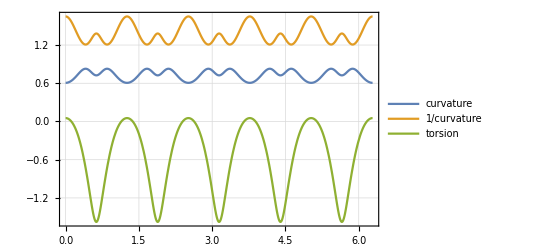

```mathematica
Clear[t,f];
f[t_]:=2{Cos[2t],Sin[2t],0}+{Cos[5t]Cos[2t],Cos[5t]Sin[2t],Sin[5t]};
{{curvature,torsion},{tangent,normal,binormal}}=Simplify[FrenetSerretSystem[f[t],t]];
Plot[{curvature,1/curvature,torsion},{t,0,2Pi},PlotRange->All,PlotTheme->"Detailed"]
```

```mathematica
Module[{a=0,b=2π,p=200,q=3,δ},
δ=(b-a)/p;
vertices=Join@@Table[f[t]+.5curvature*(Cos[2.π k/q]normal+Sin[2.π k/q]binormal)/.t->ti,{ti,a,b-δ,δ},{k,1,q}];
faceIndices=Join@@Table[Join[
MapThread[Join,{Partition[Range[(j-1)q+1,j q],2,1,{1,1}],Partition[Range[j q+1,(j+1)q],1,1]}],
MapThread[Join,{Partition[Range[(j-1)q+1,j q],1,1,{q,q}],Reverse/@Partition[Range[j q+1,(j+1)q],2,1,{1,1}]}]
],{j,1,p}];
Graphics3D[GraphicsComplex[vertices,{FaceForm[Yellow,Black],Polygon[Mod[faceIndices,Length[vertices],1]]}],Boxed->False]
]//DiscretizeGraphics
```

-Graphics3D-

```mathematica
Clear[curvature,torsion,tangent,normal,binormal,vertices,faceIndices]
```

Here we will use a mesh for the unit disk in ℝ^3 as an example. The triangles along the outer rim of the disk have an edge that is not incident with any other triangle in the mesh. All other edges in the mesh are incident with two triangles.

```mathematica
ℛ=DiscretizeGraphics[Plot3D[0,{x,y}∈Disk[],PlotPoints->1,Mesh->None]]
```

-Graphics3D-

Next we get lists of the face indices and edge indices from the mesh:

```mathematica
fa=Flatten[MeshCells[ℛ,2],Infinity,Polygon]
```

{{1,2,3},{4,5,6},{2,7,5},{4,2,5},{8,9,10},{11,8,12},{1,7,2},{13,14,15},{16,6,5},{17,13,15},{18,16,5},{19,20,21},{22,23,7},{1,3,24},{25,1,24},{1,26,8},{27,28,29},{13,30,14},{25,26,1},{13,23,30},{31,20,19},{23,20,30},{32,33,34},{35,34,33},{13,18,5},{8,26,9},{36,37,20},{7,23,5},{22,8,11},{38,39,11},{40,41,39},{22,33,42},{30,20,31},{27,42,43},{40,39,38},{44,33,39},{45,35,33},{42,46,43},{36,47,48},{49,48,50},{50,48,51},{42,33,32},{18,13,17},{42,32,46},{1,8,7},{43,52,27},{47,42,27},{23,22,47},{36,53,54},{36,48,49},{22,42,47},{55,21,20},{37,55,20},{41,44,39},{56,57,48},{29,56,27},{23,36,20},{33,44,45},{56,48,27},{37,36,54},{5,23,13},{51,48,57},{11,39,22},{49,53,36},{52,28,27},{22,39,33},{47,27,48},{12,8,10},{7,8,22},{47,36,23}}

```mathematica
ed=Flatten[MeshCells[ℛ,1],Infinity,Line]
```

{{1,2},{2,3},{3,1},{4,5},{5,6},{6,4},{2,7},{7,5},{5,2},{4,2},{8,9},{9,10},{10,8},{11,8},{8,12},{12,11},{1,7},{13,14},{14,15},{15,13},{16,6},{5,16},{17,13},{15,17},{18,16},{5,18},{19,20},{20,21},{21,19},{22,23},{23,7},{7,22},{3,24},{24,1},{25,1},{24,25},{1,26},{26,8},{8,1},{27,28},{28,29},{29,27},{13,30},{30,14},{25,26},{13,23},{23,30},{31,20},{19,31},{23,20},{20,30},{32,33},{33,34},{34,32},{35,34},{33,35},{13,18},{5,13},{26,9},{36,37},{37,20},{20,36},{23,5},{22,8},{11,22},{38,39},{39,11},{11,38},{40,41},{41,39},{39,40},{22,33},{33,42},{42,22},{31,30},{27,42},{42,43},{43,27},{38,40},{44,33},{33,39},{39,44},{45,35},{33,45},{42,46},{46,43},{36,47},{47,48},{48,36},{49,48},{48,50},{50,49},{48,51},{51,50},{32,42},{17,18},{32,46},{8,7},{43,52},{52,27},{47,42},{27,47},{22,47},{47,23},{36,53},{53,54},{54,36},{49,36},{55,21},{20,55},{37,55},{41,44},{56,57},{57,48},{48,56},{29,56},{56,27},{23,36},{44,45},{48,27},{54,37},{57,51},{39,22},{49,53},{52,28},{10,12}}

Here we see that edge 1 is a subset of precisely two faces, while edge 2 is a subset of just one face.

```mathematica
Count[SubsetQ[#,ed⟦1⟧]&/@fa,True]
```

2

```mathematica
Count[SubsetQ[#,ed⟦2⟧]&/@fa,True]
```

1

Here is a list, one item for each edge in the list ed, indicating how many faces each edge lies on:

```mathematica
Table[Count[SubsetQ[#,ed⟦k⟧]&/@fa,True],{k,Length[ed]}]
```

{2,1,2,2,2,1,2,2,2,1,2,1,2,2,2,1,2,2,1,2,1,2,2,1,1,2,2,2,1,2,2,2,1,2,2,1,2,2,2,2,1,2,2,1,1,2,2,2,1,2,2,2,2,1,1,2,2,2,1,2,2,2,2,2,2,2,2,1,1,2,2,2,2,2,1,2,2,2,1,2,2,2,1,2,2,1,2,2,2,2,2,1,2,1,2,1,1,2,1,2,2,2,2,2,2,1,2,2,1,2,1,1,1,2,2,1,2,2,1,2,1,1,2,1,1,1}

Here are the positions in the edge list of the edges that lie on only one triangle. We see that these are indeed the edges that lie on the boundary of the disk.

```mathematica
Position[%,1]//Flatten
```

{2,6,10,12,16,19,21,24,25,29,33,36,41,44,45,49,54,55,59,68,69,75,79,83,86,92,94,96,97,99,106,109,111,112,113,116,119,121,122,124,125,126}

```mathematica
HighlightMesh[ℛ,{1,#}&/@%]
```

-Graphics3D-

Here is another method for doing the same thing:

```mathematica
Count[#,True]&/@Transpose[Outer[ContainsAll,fa,ed,1]]
```

{2,1,2,2,2,1,2,2,2,1,2,1,2,2,2,1,2,2,1,2,1,2,2,1,1,2,2,2,1,2,2,2,1,2,2,1,2,2,2,2,1,2,2,1,1,2,2,2,1,2,2,2,2,1,1,2,2,2,1,2,2,2,2,2,2,2,2,1,1,2,2,2,2,2,1,2,2,2,1,2,2,2,1,2,2,1,2,2,2,2,2,1,2,1,2,1,1,2,1,2,2,2,2,2,2,1,2,2,1,2,1,1,1,2,2,1,2,2,1,2,1,1,2,1,1,1}

```mathematica
Clear[ℛ,fa,ed]
```

We begin by looking up the vertices and edges for the truncated tetrahedron:

```mathematica
v=PolyhedronData["TruncatedTetrahedron","Vertices"]
```

{{0,-1,-(√(3/2))/2},{0,1,-(√(3/2))/2},{-1/(√3),-1,1/(2 √6)},{-1/(√3),1,1/(2 √6)},{-1/(2 √3),-1/2,5/(2 √6)},{-1/(2 √3),1/2,5/(2 √6)},{1/(√3),0,5/(2 √6)},{2/(√3),0,1/(2 √6)},{-(√3)/2,-1/2,-(√(3/2))/2},{-(√3)/2,1/2,-(√(3/2))/2},{(√3)/2,-1/2,-(√(3/2))/2},{(√3)/2,1/2,-(√(3/2))/2}}

```mathematica
e=PolyhedronData["TruncatedTetrahedron","Edges"]
```

{{1,3},{1,9},{1,11},{2,4},{2,10},{2,12},{3,5},{3,9},{4,6},{4,10},{5,6},{5,7},{6,7},{7,8},{8,11},{8,12},{9,10},{11,12}}

Sanity check (and we will use this later to build the cylinders):

```mathematica
mesh=MeshRegion[v,Line[e]]
```

-Graphics3D-

Build the balls and cylinders, take their union, discretize the result and use the boundary mesh:

```mathematica
With[{radius=.11},
balls=Ball[#,radius]&/@v;
cylinders=MeshPrimitives[mesh,1]/.Line[pts_]:>Cylinder[pts,radius]
];
```

```mathematica
ru=RegionUnion@@Join[cylinders,balls];
```

```mathematica
truncatedTetrahedron=RegionBoundary[DiscretizeRegion[ru,MaxCellMeasure->{"Length"->.03}]]
```

-Graphics3D-

```mathematica
Clear[v,e,mesh,balls,cylinders,ru,truncatedTetrahedron]
```

This is much like the previous exercise. Note that we multiply all vertex coordinates by 10 to make a larger model.

```mathematica
v=PolyhedronData["TetrahedronFiveCompound","Vertices"];
e=PolyhedronData["TetrahedronFiveCompound","Edges"];
mesh=MeshRegion[10v,Line[e]]
```

-Graphics3D-

```mathematica
With[{radius=.4},
balls=Ball[#,radius]&/@MeshCoordinates[mesh];
cylinders=MeshPrimitives[mesh,1]/.Line[pts_]:>Cylinder[pts,radius];
]
```

```mathematica
RegionBoundary[DiscretizeRegion[RegionUnion@@Join[cylinders,balls],MaxCellMeasure->{"Length"->.3}]]
```

-Graphics3D-

```mathematica
Clear[v,e,mesh,balls,cylinders]
```

We follow the examples in this section, adjusting PlotPoints to give a mesh with good fidelity.

```mathematica
torusKnot[m_,n_][t_]:=2{Cos[m t],Sin[m t],0}+{Cos[m t]Cos[n t],Sin[m t]Cos[n t],Sin[n t]}
```

```mathematica
ParametricPlot3D[s*torusKnot[2,5][t+π]+(1-s)torusKnot[2,5][t],{t,0,π},{s,0,1},Mesh->All,MaxRecursion->0,PlotPoints->{100,10},PlotStyle->{Thickness[.15],FaceForm[Yellow,Black]},Boxed->False,Axes->False,ImageSize->250]
```

-Graphics3D-

We follow the examples in this section, and simply add a Sphere at (2,0,0) of radius 0.7 (it must be smaller than the space defined by the Tube).

```mathematica
torusKnot[m_,n_][t_]:=2{Cos[m t],Sin[m t],0}+{Cos[m t]Cos[n t],Sin[m t]Cos[n t],Sin[n t]}
```

```mathematica
wireframeTorus=ParametricPlot3D[torusKnot[9,1][t],{t,0,2π+.1},MaxRecursion->0,PlotPoints->500,PlotStyle->Tube[.15,PlotPoints->30],Boxed->False,Axes->False,PlotRange->All];
ball=Graphics3D[Sphere[{2,0,0},.7]];
Show[wireframeTorus,ball]
```

-Graphics3D-

```mathematica
Clear[torusKnot,wireframeTorus,ball]
```

Yes, this mesh is watertight—it has no defects!

```mathematica
ChemicalData["Caffeine","MeshRegion"]//FindMeshDefects
```

-Graphics3D-

### Section 9.6

We follow the same steps that were used for the Penrose kite tile, beginning with the measurements given in the figure.

```mathematica
SASTriangle[1+GoldenRatio,36 Degree,1+1/GoldenRatio]//FullSimplify
```

Triangle[{{0,0},{1/2 (1+√5),0},{-1/2,1/2 √(5+2 √5)}}]

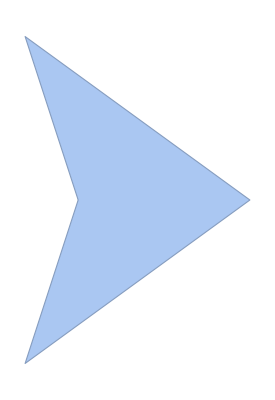

```mathematica
dart2D=BoundaryMeshRegion[{{0,0},{-1/2,1/2 √(5+2 √5)},{1/2 (1+√5),0},{-1/2,-1/2 √(5+2 √5)}},Line[{1,4,3,2,1}]]
```

```mathematica
dartWalls=RegionProduct[RegionBoundary[dart2D],Line[{{0},{.1}}]]
```

-Graphics3D-

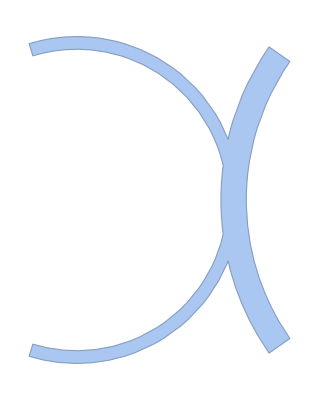

```mathematica
With[{δ=.1},arc1=DiscretizeGraphics[Annulus[{0,0},{1/GoldenRatio-δ/4,1/GoldenRatio+δ/4},{-107Degree,107Degree}]];
arc2=DiscretizeGraphics[Annulus[{1/2 (1+√5),0},{1-δ/2,1+δ/2},{145Degree,(144+71)Degree}]];
dartArcs=RegionUnion[arc1,arc2]]
```

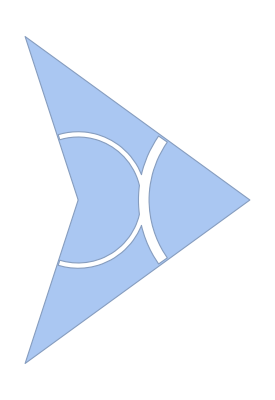

```mathematica
dart2Dtop=RegionDifference[dart2D,dartArcs]
```

```mathematica
arcWalls=RegionProduct[RegionBoundary[dartArcs],Line[{{.1},{.2}}]]
```

-Graphics3D-

```mathematica
dart3D=DiscretizeGraphics[Show[
RegionProduct[dart2D,Point[{0.}]],
dartWalls,
RegionProduct[dart2Dtop,Point[{.1}]],
arcWalls,
RegionProduct[dartArcs,Point[{.2}]]
]]
```

-Graphics3D-

```mathematica
HighlightMesh[RepairMesh[dart3D,"FlippedFaces"],Style[2,FaceForm[Yellow,Black]]]
```

-Graphics3D-

```mathematica
Clear[dart2D,dartWalls,arc1,arc2,dartArcs,dart2Dtop,arcWalls,dart3D]
```

We use the example in this section to produce the text, and follow the steps from the previous problem to construct the mesh. Note that before defining the rectangle used for the base plate, we look up the RegionBounds for the text (presented in the form {{xmin,xmax},{ymin,ymax}}) and use slightly larger bounds for the Rectangle (in the form {{xmin,xmax},{ymin,ymax}}).

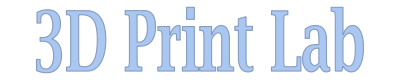

```mathematica
text="3D Print Lab";
meshText=BoundaryDiscretizeGraphics[Text[Style[text,FontFamily->"Lucida Bright",FontWeight->Bold]],_Text]
```

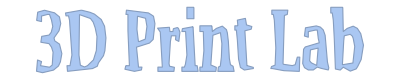

```mathematica
meshTextDegraded=Nest[ImageMesh[RegionImage[#]]&,meshText,4]
```

```mathematica
RegionBounds[meshTextDegraded]
```

{{16.511,343.709},{2.0822,48.}}

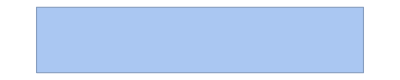

```mathematica
rectangle=DiscretizeGraphics[Rectangle@@{{14,0},{346,50}}]
```

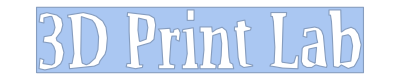

```mathematica
rectangleTop=RegionDifference[rectangle,meshTextDegraded]
```

```mathematica
rectangleSides=RegionProduct[RegionBoundary[rectangle],Line[{{-5.},{0.}}]]
```

-Graphics3D-

```mathematica
textSides=RegionProduct[RegionBoundary[meshTextDegraded],Line[{{0.},{10.}}]]
```

-Graphics3D-

```mathematica
model=DiscretizeGraphics[Show[
RegionProduct[meshTextDegraded,Point[{10.}]],
textSides,
RegionProduct[rectangleTop,Point[{0.}]],
rectangleSides,
RegionProduct[rectangle,Point[{-5.}]]
]]
```

-Graphics3D-

```mathematica
HighlightMesh[RepairMesh[model,"FlippedFaces"],Style[2,FaceForm[Yellow,Black]]]
```

-Graphics3D-

```mathematica
Clear[text,meshText,meshTextDegraded,rectangle,rectangleTop,rectangleSides,textSides,model]
```

We begin by producing a 2D BoundaryMeshRegion for each letter.

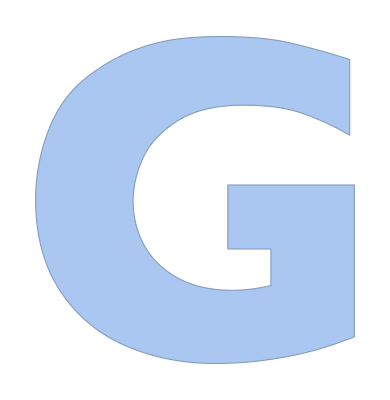
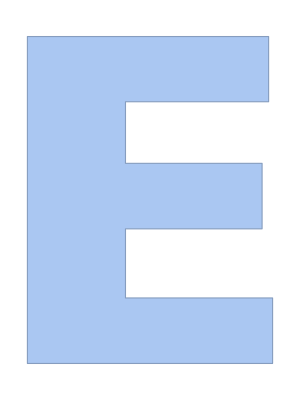
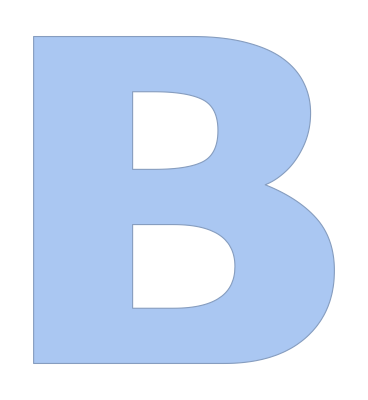

```mathematica
{g,e,b}=BoundaryDiscretizeGraphics[Text[Style[#,FontFamily->"Gill Sans",Bold]],_Text]&/@{"G","E","B"}
```

```mathematica
RegionBounds/@{g,e,b}//Column
```

{{-3.18219,3.18219},{-3.2575,3.2575}}
{{-2.38737,2.38737},{-3.18219,3.18219}}
{{-2.90141,2.90141},{-3.15294,3.15294}}

We will rescale these so that each letter fits in a perfect square with bounds {{-1,1},{-1,1}}. So given a BoundaryMeshRegion whose bounds are of the form {{-a,a},{-b,b}}, we will scale the x coordinate by 1/a, and scale the y coordinate by 1/b.

```mathematica
normalize[mesh_]:=Module[{rb=RegionBounds[mesh]},
BoundaryMeshRegion[{1/rb⟦1,2⟧,1/rb⟦2,2⟧}*#&/@MeshCoordinates[mesh],MeshCells[mesh,1],Axes->True]]
```

And any letter may be reflected through the x axis or the y axis, or rotated 90° or 180°. For this cube, reflecting the “G” through the y axis works nicely.

```mathematica
reflectY[mesh_]:=BoundaryMeshRegion[MeshCoordinates[mesh]/.{x_,y_}->{-x,y},MeshCells[mesh,1],Axes->True]
```

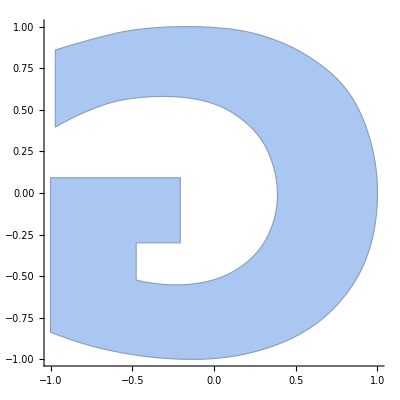
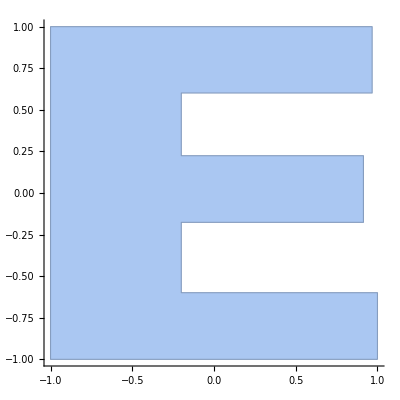
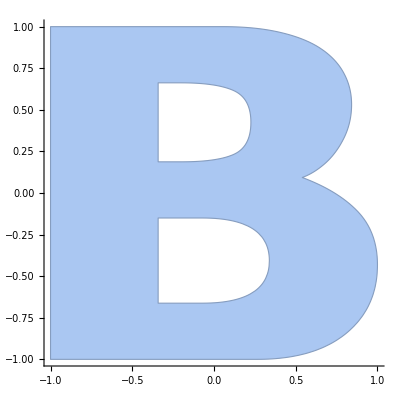

```mathematica
g2D=reflectY[normalize[g]];
e2D=normalize[e];
b2D=normalize[b];
{g2D,e2D,b2D}
```

```mathematica
g3D=RegionProduct[Line[{{-1.},{1.}}],g2D];
e3D=RegionProduct[e2D,Line[{{-1.},{1.}}]];
e3D=MeshRegion[MeshCoordinates[e3D]/.{x_,y_,z_}->{x,z,y},MeshCells[e3D,3]];
b3D=RegionProduct[b2D,Line[{{-1.},{1.}}]];
threeD=RegionIntersection[g3D,e3D,b3D]
```

-Graphics3D-

```mathematica
{Show[threeD,ViewPoint->Left],Show[threeD,ViewPoint->Front],Show[threeD,ViewPoint->Top]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Clear[g,e,b,normalize,reflectY,g2D,e2d,b2d,g3d,e3d,b3d,threeD]
```

The bounds on u determine the height of the extruded curve.

```mathematica
ParametricPlot3D[{Sin[t],Cos[3t],u},{t,0,2π+.1},{u,0,.2},PlotStyle->Thickness[.1],PlotPoints->{100,3},MaxRecursion->0,Mesh->All]
```

-Graphics3D-

There are 114=6 19 images, so we place six images per row and make a GraphicsGrid of the full list of lamina. Everything here is easily extruded into a 3D model.

```mathematica
images=#["Image"]&/@LaminaData[];
```

```mathematica
Length[images]//FactorInteger
```

{{2,1},{3,1},{19,1}}

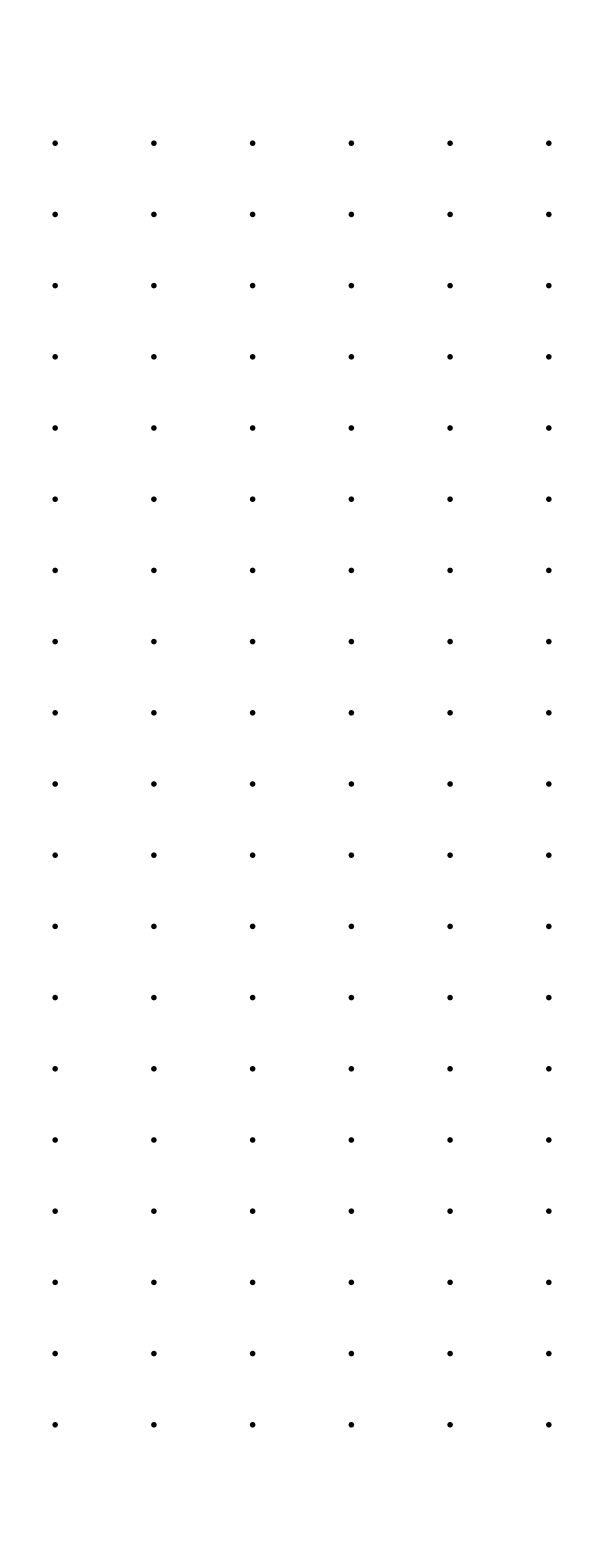

```mathematica
GraphicsGrid[Partition[images,6]]
```

```mathematica
Clear[images]
```

### Section 9.7

We follow the same procedure outlined in this section.

```mathematica
Reduce[x^2-2x==x,x]
```

x==0||x==3

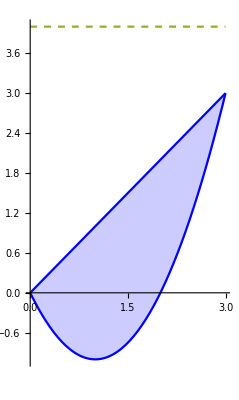

```mathematica
Plot[{x,x^2-2x,4},{x,0,3},PlotRange->{-1,4},AspectRatio->Automatic,Filling->{1->{2}},PlotStyle->{Blue,Blue,Dashed}]
```

The distance from a point (x,y,z) in space to the line y=4 in the xy plane is √((y-4)^2+z^2). So for (x,y,z) to lie on the surface of the solid of revolution, this distance must be either 4-x or 4-(x^2-2x). Hence:

```mathematica
ℛ=ImplicitRegion[(4-x)^2==(y-4)^2+z^2||(4-(x^2-2x))^2==(y-4)^2+z^2,{{x,0,3},y,z}];
```

```mathematica
dRev=DiscretizeRegion[ℛ,MaxCellMeasure->.05]
```

-Graphics3D-

```mathematica
HighlightMesh[RepairMesh[dRev,"FlippedFaces"],Style[2,FaceForm[Yellow,Black]]]
```

-Graphics3D-

```mathematica
Clear[ℛ,dRev]
```

This is more challenging than the previous exercise if the goal is a watertight mesh. We first show how to use RevolutionPlot3D to produce a non-watertight mesh (with two connected components). That will suffice for most FDM printers.

```mathematica
Reduce[x^2-2x==x,x]
```

x==0||x==3

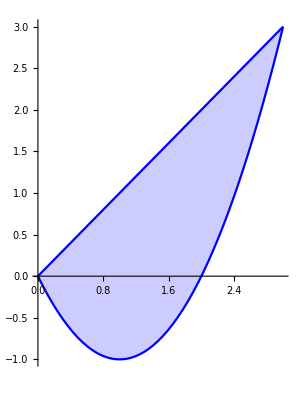

```mathematica
Plot[{x,x^2-2x},{x,0,3},AspectRatio->Automatic,PlotStyle->Blue,Filling->{1->{2}},AxesStyle->{Automatic,Dashed}]
```

```mathematica
RevolutionPlot3D[{{x},{x^2-2x}},{x,0,3},Mesh->None]//DiscretizeGraphics
```

DiscretizeGraphics::prng: Value of option PlotRange -> {{Automatic,Automatic},{Automatic,Automatic},{Automatic,Automatic}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

-Graphics3D-

We next go about building a watertight mesh. The distance from a point (x,y,z) to the y axis is √(x^2+z^2).  The distance from the parabola to the y axis depends on whether you are on the left branch or the right. Solve for the x coordinate to get the distance to the y axis.

```mathematica
Solve[y==x^2-2x,x]
```

{{x→1-√(1+y)},{x→1+√(1+y)}}

So for (x,y,z) to lie on the surface of revolution generated by the parabola, the distance to the y axis must be either 1-√(1+y) or 1+√(1+y).  For (x,y,z) to lie on the surface of the solid generated by the cone, this distance must be y. Hence we may describe the surface as the union of three pieces, each dependent on the value of y:

```mathematica
ℛ=ImplicitRegion[(x^2+z^2==y^2&&y≥0)||(x^2+z^2==(1+√(1+y))^2&&-1≤y≤3)||(x^2+z^2==(1-√(1+y))^2&&-1≤y≤0),{x,y,z}];
```

```mathematica
DiscretizeRegion[ℛ]
```

DiscretizeRegion::drf: DiscretizeRegion was unable to discretize the region ImplicitRegion[«2»].

DiscretizeRegion[ImplicitRegion[(x^2+z^2==y^2&&y≥0)||(x^2+z^2==(1+√(1+y))^2&&-1≤y≤3)||(x^2+z^2==(1-√(1+y))^2&&-1≤y≤0),{x,y,z}]]

Unfortunately, DiscretizeRegion (as of Mathematica version 12.0) cannot handle the region ℛ. But we can work around this by breaking the region into two parts, one for the cone and one for the rotated parabola. Then take the union and discretize.

```mathematica
ℛ1=ImplicitRegion[(x^2+z^2==(1+√(1+y))^2&&-1≤y≤3)||(x^2+z^2==(1-√(1+y))^2&&-1≤y≤0),{x,y,z}];
```

```mathematica
dRev1=DiscretizeRegion[ℛ1]
```

-Graphics3D-

```mathematica
ℛ2=ImplicitRegion[(x^2+z^2==y^2&&0≤y≤3),{x,y,z}];
```

```mathematica
dRev2=DiscretizeRegion[ℛ2]
```

-Graphics3D-

```mathematica
ru=RegionUnion[ℛ1,ℛ2];
DiscretizeRegion[ru]
```

-Graphics3D-

Finally, we perform some diagnostics to clean things up: We see that there is only one connected component. That’s good.

```mathematica
ConnectedMeshComponents[DiscretizeRegion[ru]]
```

{-Graphics3D-}

But there are some flipped faces, and of course there is a singular vertex (the triangles incident with this vertex do not form a topological disk, rather they form two disks joined at a point—one disk is comprised of triangles from the cone, and the other is comprised of triangles on the parabolic surface.

```mathematica
FindMeshDefects[DiscretizeRegion[ru]]
```

-Graphics3D-

```mathematica
HighlightMesh[RepairMesh[DiscretizeRegion[ru]],Style[2,FaceForm[Yellow,Black]]]
```

-Graphics3D-

Unfortunately, RepairMesh flipped the wrong faces. We can apply flipFaces to the result to fix things.

```mathematica
flipFaces[mesh_]:=
MeshRegion[MeshCoordinates[mesh],Polygon[Reverse@@@MeshCells[mesh,2]]]
```

```mathematica
HighlightMesh[flipFaces@RepairMesh[DiscretizeRegion[ru]],Style[2,FaceForm[Yellow,Black]]]
```

-Graphics3D-

```mathematica
Clear[ℛ,ℛ1,ℛ2,dRev1,dRev2,ru]
```

Begin with a nice picture:

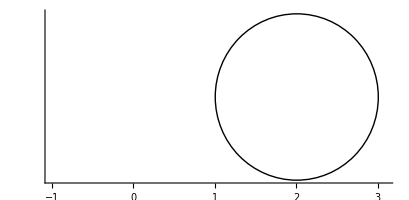

```mathematica
Graphics[Circle[{2,0},1],PlotRange->{{-1,3.1},Automatic},Axes->True,AxesStyle->{Automatic,Dashed},Ticks->{Automatic,None}]
```

Let us first find an expression for the distance from a point (x,y) on the circle circle above to the y axis, expressed as a function of y, where -1≤y≤1. Noting that for any point (x,y), the distance to the y axis is simply x, we solve the circle equation for x. There are two solutions, one for the left half of the circle (where x≤2) and one for the right half.

```mathematica
Reduce[(x-2)^2+y^2==1,x]
```

x==2-√(1-y^2)||x==2+√(1-y^2)

If a point (x,y,z) lies on the surface of the torus, its distance to the y axis must therefore be one of 2-√(1-y^2) or 2+√(1-y^2). But the distance from any point (x,y,z) to the y axis is simply √(x^2+z^2). Hence we get the implicit equation below for the torus. Note that we constrain y to lie between -1 and 1.

```mathematica
ℛ=ImplicitRegion[√(x^2+z^2)==2-√(1-y^2)||√(x^2+z^2)==2+√(1-y^2),{x,{y,-1,1},z}];
```

```mathematica
dRev=DiscretizeRegion[ℛ,MaxCellMeasure->.05]
```

-Graphics3D-

```mathematica
FindMeshDefects[dRev]
```

-Graphics3D-

```mathematica
torus=RepairMesh[dRev,"FlippedFaces"];
HighlightMesh[torus,Style[2,FaceForm[Yellow,Black]]]
```

-Graphics3D-

RepairMesh flipped the wrong faces, so we apply flipFaces to the result.

```mathematica
flipFaces[mesh_]:=
MeshRegion[MeshCoordinates[mesh],Polygon[Reverse@@@MeshCells[mesh,2]]]
```

```mathematica
HighlightMesh[flipFaces[torus],Style[2,FaceForm[Yellow,Black]]]
```

-Graphics3D-

```mathematica
Clear[ℛ,dRev,torus,flipFaces]
```

### Section 9.8

A simple replacement rule is all that’s needed. We replace every positive entry x with x+10.

```mathematica
testData=Table[RandomInteger[{-50,50}],{5},{5}];
testData//MatrixForm
```

(15 | 44 | -22 | 45 | -3
1 | 19 | -37 | 40 | 7
9 | 33 | -34 | 14 | 5
28 | -46 | 28 | -15 | -39
19 | 37 | 43 | 43 | 14)

```mathematica
testData/.x_?Positive->x+10//MatrixForm
```

(25 | 54 | -22 | 55 | -3
11 | 29 | -37 | 50 | 17
19 | 43 | -34 | 24 | 15
38 | -46 | 38 | -15 | -39
29 | 47 | 53 | 53 | 24)

```mathematica
Clear[testData]
```